## Getting started: HyperBloch package

This is a notebook for the first steps for the use of the HyperBloch package for efficient modeling of tight-binding models on hyperbolic lattices.

## Preliminaries:

### Remark:

Before using the getting started with the HyperBloch notebook:

Make sure that the HyperBloch package is installed, if this is not the case please follow the instruction on the website (link to website ???).

Make sure that the required files .hcc, .hcm and .hcs files are in the current directory. This entails files:

(2,8,8)_T2.6_3.hcc

{8,8}-tess_T2.6_3.hcm

(2,8,8)_T3.11_3.hcc

{8,8}-tess_T2.6_3_sc-T3.11.hcs

In case no such files exists, please follow the instructions in the the prerequisites section on the website (link to website ???) or download it there.

### Load the HyperBloch package:

```mathematica
<<PatrickMLenggenhager`HyperBloch`
```

Open the documentation:

```mathematica
Documentation`HelpLookup["PatrickMLenggenhager/HyperBloch/tutorial/BasicUsage"];
```

```mathematica
Documentation`HelpLookup["PatrickMLenggenhager/HyperBloch/guide/HyperBlochPackage"];
```

## Primitive cell:

### Import:

Load the previously exported HyperCells data from the current directory:

```mathematica
SetDirectory[NotebookDirectory[]];

pcell=ImportCellGraphString[Import["(2,8,8)_T2.6_3.hcc"]];
pcmodel=ImportModelGraphString[Import["{8,8}-tess_T2.6_3.hcm"]];
```

### Visualization:

Visualize the model on the primitive cell:

```mathematica
VisualizeModelGraph[pcmodel,
Elements-><|
			ShowCellGraphFlattened->{},
			ShowCellBoundary->{ShowEdgeIdentification->True}
		|>,

CellGraph->pcell,
NumberOfGenerations->2,
ImageSize->300]
```

-Graphics-

### General strategy construction of the Hamiltonian:

To construct the Abelian Bloch Hamiltonian, we need to assign the parameters to vertices and edges in the cell graph model. This takes a very compact form for a simple nearest neighbour tight-binding model. In order to illustrate the procedure, we will start with the most general assignment strategy and demonstrate the compact form afterwards

#### Number of orbitals:

The HyperBloch package supports the construction of models with multiple orbits per site and allows for different numbers of orbitals per site as well. For now, we will set the number of orbitals to one, and postpone the discussion to the next section.

```mathematica
norbits = 1;
```

#### Onsite terms:

Onsite terms in the Hamiltonian are associated with vertices in the cell graph model. It is useful to explicitly  print the vertices using the VertexListpaclet:ref/VertexList function of Mathematica:

```mathematica
VertexList@pcmodel["Graph"]
```

{{3,1}}

As expected for the hyperbolic {8,8}-lattice there is one vertex corresponding to 1 site within the primitive cell.  We will set the onsite terms to zero by associating the vertices with a zero vector.

```mathematica
mVec =ConstantArray[0,1]; 
onsitePC=AssociationThread[VertexList@pcmodel["Graph"]->mVec];
```

#### Hopping terms:

The hopping terms for nearest neighbour interactions are associated with edges in the cell graph model. Similarly to the onsite terms, it is useful to explicitly print the edges using  EdgeListpaclet:ref/EdgeList function of Mathematica:

```mathematica
EdgeList@pcmodel["Graph"]
```

{{3,1}{3,1}{1,{1,1,5}},{3,1}{3,1}{1,{2,4,8}},{3,1}{3,1}{1,{3,2,6}},{3,1}{3,1}{1,{4,3,7}}}

Each element in the list is a DirectedEdgepaclet:ref/DirectedEdge,describing an association of pairs of vertices with one another. More concretely, the nested list above the arrows of the form  {1, {ve, s1, s2}}consist of entries which identify the position of the edge within the primitive cell (see HCModelGraphpaclet:PatrickMLenggenhager/HyperBloch/ref/HCModelGraphPatrickMLenggenhager Package Symbol).

It might also be helpful to look at the translation operators associated with the edges :

```mathematica
pcmodel["EdgeTranslations"]
```

{g1,g4,g2,g3}

We will now set the hopping terms to a constant real value -1 for all edges by associating the edge list with a list of constant values.

```mathematica
nnHoppingVec=ConstantArray[-1,4];
hoppingPC=AssociationThread[EdgeList@pcmodel["Graph"]->nnHoppingVec];
```

The HyperBloch package incorporates elaborate visualizations of cell graphs and cell graph models which can further guide the construction of models in more advanced settings. We will exploit these in subsequent tutorials.

The Hamiltonian can now be set up by specifying the model graph and the corresponding coupling constants specified above.

```mathematica
Hpc=AbelianBlochHamiltonianExpression[pcmodel,norbits,onsitePC,hoppingPC];
```

```mathematica
FullSimplify[AbelianBlochHamiltonianExpression[pcmodel,norbits,onsitePC,hoppingPC,k]]
```

{{-2 (Cos[k[1]]+Cos[k[2]]+Cos[k[3]]+Cos[k[4]])}}

### Compact construction of the Hamiltonian:

The simplicity of the specified model reduces the construction of the Hamiltonian to just one line of code:

```mathematica
Hpc=AbelianBlochHamiltonian[pcmodel,1,0&,-1&];
```

Compile it for more efficient evaluation:

```mathematica
Hpc=AbelianBlochHamiltonian[pcmodel,1,0&,-1&,CompileFunction->True];
```

### Density of states:

Compute the density of states:

```mathematica
ComputeEigenvalues[cfH_,Npts_,Nruns_]:=Module[{dimk=Length[cfH[[2]]]},
Flatten@ParallelTable[
Flatten@Table[
Eigenvalues[cfH@@RandomReal[{-Pi,Pi},dimk]],{i,1,Round[Npts/Nruns]}],
{j,1,Nruns},Method->"FinestGrained"]]
```

```mathematica
evspc=ComputeEigenvalues[Hpccf,10^6,32];
```

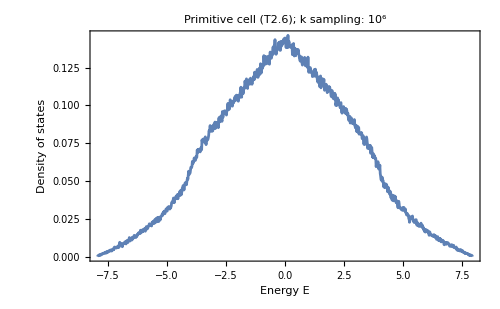

```mathematica
SmoothHistogram[evspc,0.005,"PDF",Frame->True,FrameStyle->Black,FrameLabel->{"Energy E","Density of states"},PlotRange->All, LabelStyle->20,PlotLabel->"Primitive cell (T2.6); k sampling: 10^6",ImageSize->500,ImagePadding->{{Automatic, 10}, {Automatic, 10}},Background->None]
```

## Supercell:

### Import:

Load the previously exported HyperCells data from the current directory :

```mathematica
scell=ImportCellGraphString[Import["(2,8,8)_T3.11_3.hcc"]];
scmodel=ImportSupercellModelGraphString[Import["{8,8}-tess_T2.6_3_sc-T3.11.hcs"]];
```

### Visualization:

```mathematica
VisualizeModelGraph[scmodel,
Elements-><|
			ShowCellGraphFlattened->{},
			ShowCellBoundary->{ShowEdgeIdentification->True}
		|>,

CellGraph->scell,
NumberOfGenerations->3,
ImageSize->300]
```

Det::luc: Result for Det of badly conditioned matrix {{0.594604,-0.246293},{0.840896,-0.348311}} may contain significant numerical errors.

Det::luc: Result for Det of badly conditioned matrix {{0.594604,0.246293},{0.840896,0.348311}} may contain significant numerical errors.

Det::luc: Result for Det of badly conditioned matrix {{0.246293,-0.594604},{0.348311,-0.840896}} may contain significant numerical errors.

General::stop: Further output of Det::luc will be suppressed during this calculation.

-Graphics-

### Hamiltonian and density of states:

Compute the density of states on the supercell:

```mathematica
Hsc=AbelianBlochHamiltonian[scmodel,1,0&,-1&,PCModel->pcmodel,CompileFunction->True];
```

```mathematica
evssc=ComputeEigenvalues[Hsc,2 10^5,32];
```

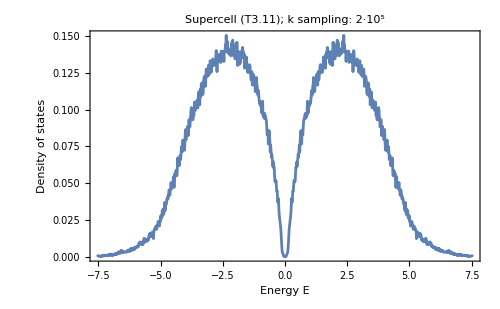

```mathematica
SmoothHistogram[evssc,0.005,"PDF",Frame->True,FrameStyle->Black,FrameLabel->{"Energy E","Density of states"},PlotRange->All,LabelStyle->20,PlotLabel->"Supercell (T3.11); k sampling: 2·10^5",ImageSize->500,ImagePadding->{{Automatic, 10}, {Automatic, 10}},Background->None]
```

```mathematica
NotebookSave[]
```